This is for Vv256

The exercises for the Tuesday’s class.

中文参考
-Graphics-
-Graphics-

Olga 课件
-Graphics-

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

1/((1-y) (3-y))

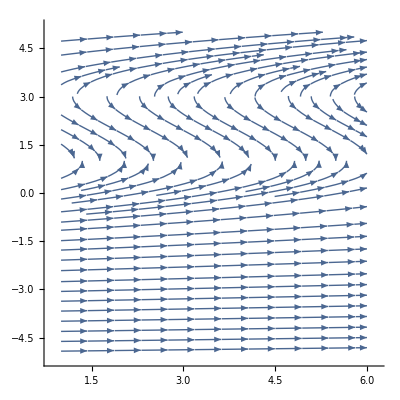

```mathematica
f[x_,y_]=1/((1-y)*(3-y))

StreamPlot[{1,f[x,y]},{x,1,6},{y,-5,5},Frame->False,Axes->True]
```

7+8 y+y^2

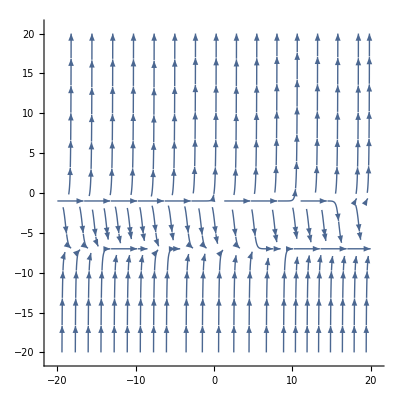

```mathematica
f[x_,y_]=(y^2+8*y+7)

StreamPlot[{1,f[x,y]},{x,-20,20},{y,-20,20},Frame->False,Axes->True]
```

-4 y+y^2/5

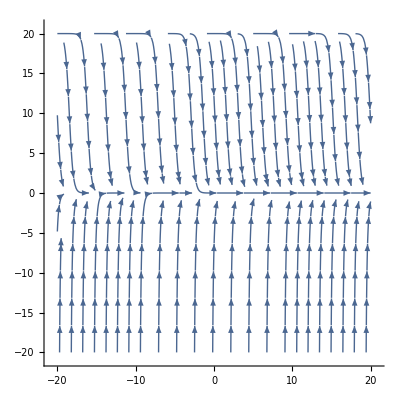

```mathematica
f[x_,y_]=y^2/5-4*y

StreamPlot[{1,f[x,y]},{x,-20,20},{y,-20,20},Frame->False,Axes->True]
```

解微分方程实例

```mathematica
DSolve[y'[x]==x,y[x],x]
```

{{y[x]→x^2/2+C[1]}}

```mathematica
DSolve[y'[x]==(1+3*x^2)/(3*y[x]^2-6*y[x]),y[x],x]
```

{{y[x]→1+(3 2^(1/3))/(54+27 x+27 x^3+81 C[1]+√(-2916+(54+27 x+27 x^3+81 C[1])^2))^(1/3)+1/(3 2^(1/3))(54+27 x+27 x^3+81 C[1]+√(-2916+(54+27 x+27 x^3+81 C[1])^2))^(1/3)},{y[x]→1-(3 (1+ⅈ √3))/(2^(2/3) (54+27 x+27 x^3+81 C[1]+√(-2916+(54+27 x+27 x^3+81 C[1])^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (54+27 x+27 x^3+81 C[1]+√(-2916+(54+27 x+27 x^3+81 C[1])^2))^(1/3)},{y[x]→1-(3 (1-ⅈ √3))/(2^(2/3) (54+27 x+27 x^3+81 C[1]+√(-2916+(54+27 x+27 x^3+81 C[1])^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (54+27 x+27 x^3+81 C[1]+√(-2916+(54+27 x+27 x^3+81 C[1])^2))^(1/3)}}

```mathematica
DSolve[y[x]=x*y'[x]+y'[x]+Sqrt[y'[x]],y[x],x]
```

$RecursionLimit::reclim2: 在 y'[x]+sin y'[x] 计算过程中超过 1024 的递归深度.

Hold[DSolve[y[x]=x y'[x]+y'[x]+√y'[x],y[x],x]]

```mathematica
DSolve[2*x^2*y'[x]==(x-1)*(y[x]^2-x^2)+2*x*y[x],y[x],x]
```

{{y[x]→(x (-ⅇ^(x+2 C[1])+x))/(ⅇ^(x+2 C[1])+x)}}